#### Datos de columnas II y III de tableta Plimpton322

```mathematica
Tablet={
{{1,59},{2,49}},
{{56,7},{1,20,25}},
{{1,16,41},{1,50,49}},
{{3,31,49},{5,9,1}},
{{1,5},{1,37}},
{{5,19},{8,1}},
{{38,11},{59,1}},
{{13,19},{20,49}},
{{8,1},{12,49}},
{{1,22,41},{2,16,1}},
{{45},{1,15}},
{{27,59},{48,49}},
{{2,41},{4,49}},
{{29,31},{53,49}},
{{28},{53}}
};
```

#### Funciones

```mathematica
DecimalFloat[n_]:=FromDigits[Reverse[n],1/60]//N
CalcBetaSq[b_,d_]:=(FromDigits[b,60]/Sqrt[FromDigits[d,60]^2-FromDigits[b,60]^2])^2//N
CalcBeta[b_,d_]:=FromDigits[b,60]/Sqrt[FromDigits[d,60]^2-FromDigits[b,60]^2]//N
CalcDelta[b_,d_]:=FromDigits[d,60]/Sqrt[FromDigits[d,60]^2-FromDigits[b,60]^2]//N
Calcl[b_,d_]:=Sqrt[FromDigits[d,60]^2-FromDigits[b,60]^2]//N
Triangle322[b_,d_]:=Graphics[{FaceForm[{White,Opacity[0.0]}],EdgeForm[Thick],White,Polygon[{{0,0},{0,Calcl[b,d]},{-FromDigits[b,60],0}}]}];
Triangle322[b_,d_,t_]:=Graphics[{FaceForm[{White,Opacity[0.0]}],EdgeForm[Thick],White,Polygon[{{0,0},{0,Calcl[b,d]},{-FromDigits[b,60],0}}],Text[t,{-FromDigits[b,60]/4,Calcl[b,d]/2},BaseStyle->{Small,Red,FontFamily->"Courier"}]},PlotRange->{{-14000,100},{-100,15000}},ImageSize->600];
```

```mathematica
Triangle322N[b_,d_]:=Graphics[{FaceForm[{White,Opacity[0.1]}],EdgeForm[Thick],White,Polygon[{{0,0},{0,1},{-FromDigits[b,60]/Calcl[b,d],0}}]}];
Triangle322NPrism[b_,d_]:=Graphics3D[{FaceForm[{White,Opacity[0.1]}],EdgeForm[Thick],White,Prism[{{0,0,0},{0,1,0},{-FromDigits[b,60]/Calcl[b,d],0,0},{0,0,0.1},{0,1,0.1},{-FromDigits[b,60]/Calcl[b,d],0,0.1}}]}];
Triangle322N[b_,d_,t_]:=Graphics[{FaceForm[{White,Opacity[0.1]}],EdgeForm[Thick],White,Polygon[{{0,0},{0,1},{-FromDigits[b,60]/Calcl[b,d],0}}],Text[t,{(-FromDigits[b,60]/Calcl[b,d])/4,0.5},BaseStyle->{Small,Red}]},
PlotRange->{{-1.1,0.1},{-0.1,1.1}},ImageSize->600];
```

#### Cálculos de Ejemplo

```mathematica
DecimalFloat[{0,59,0,15}]
```

0.983403

```mathematica
CalcBetaSq[{1,59},{2,49}]
```

0.983403

```mathematica
CalcBetaSq[{56,7},{1,20,25}]
DecimalFloat[{0,56,56,58,14,50,6,15}]
```

0.949159

0.949159

```mathematica
FromDigits[{3,31,49},60]
```

12709

```mathematica
FromDigits[{1,2},60]
```

62

```mathematica
Calcl[{3,31,49},{5,9,1}]
```

13500.

#### Construyendo los triangulos normalizados

```mathematica
Triangle322N[{3,31,49},{5,9,1}]
```

-Graphics-

```mathematica
Show[Table[Triangle322N[Tablet⟦i,1⟧,Tablet⟦i,2⟧],{i,15}],ImageSize->600]
```

-Graphics-

```mathematica
Show[Table[Triangle322[Tablet⟦i,1⟧,Tablet⟦i,2⟧],{i,15}]]
```

-Graphics-

```mathematica
Manipulate[Show[Table[Triangle322[Tablet⟦i,1⟧,Tablet⟦i,2⟧,ToString[i]],{i,n}],ImageSize->350],{n,1,15}]
```

Part::partd: Part specification Tablet⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Tablet⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification Tablet⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{Triangle322[Tablet⟦1,1⟧,Tablet⟦1,2⟧,1]},ImageSize→350].

```mathematica
Manipulate[Show[Table[Triangle322N[Tablet⟦i,1⟧,Tablet⟦i,2⟧,ToString[i]],{i,n}],ImageSize->350],{n,1,15}]
```

Part::partd: Part specification Tablet⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Tablet⟦1,2⟧ is longer than depth of object.

Show::gcomb: Could not combine the graphics objects in Show[{Triangle322N[Tablet⟦1,1⟧,Tablet⟦1,2⟧,1]},ImageSize→350].

```mathematica
t=Table[Triangle322[Tablet⟦i,1⟧,Tablet⟦i,2⟧,ToString[i]],{i,15}];
```

```mathematica
t2⟦10⟧
```

-Graphics-

```mathematica
t2=Table[Triangle322N[Tablet⟦i,1⟧,Tablet⟦i,2⟧,ToString[i]],{i,15}];
```

```mathematica
SetDirectory["/Users/tomasdecaminobeck/Downloads/"]
```

/Users/tomasdecaminobeck/Downloads

```mathematica
Do[
Export["t_Norm_"<>ToString[i]<>".svg",t2⟦i⟧]
,{i,15}]
```

```mathematica
Export["t.gif",t,"DisplayDurations"->1]
```

t.gif

```mathematica
DecimalP322=Table[{CalcDelta[Tablet⟦i,1⟧,Tablet⟦i,2⟧],CalcBeta[Tablet⟦i,1⟧,Tablet⟦i,2⟧],CalcBetaSq[Tablet⟦i,1⟧,Tablet⟦i,2⟧],FromDigits[Tablet⟦i,1⟧,60],FromDigits[Tablet⟦i,2⟧,60]},{i,15}];
```

```mathematica
Grid[Table[{CalcDelta[Tablet⟦i,1⟧,Tablet⟦i,2⟧],CalcBeta[Tablet⟦i,1⟧,Tablet⟦i,2⟧],CalcBetaSq[Tablet⟦i,1⟧,Tablet⟦i,2⟧],FromDigits[Tablet⟦i,1⟧,60],FromDigits[Tablet⟦i,2⟧,60]},{i,15}]]
```

1.40833 | 0.991667 | 0.983403 | 119 | 169
1.39612 | 0.974248 | 0.949159 | 3367 | 4825
1.38521 | 0.958542 | 0.918802 | 4601 | 6649
1.37341 | 0.941407 | 0.886248 | 12709 | 18541
1.34722 | 0.902778 | 0.815008 | 65 | 97
1.33611 | 0.886111 | 0.785193 | 319 | 481
1.31148 | 0.848519 | 0.719984 | 2291 | 3541
1.30104 | 0.832292 | 0.692709 | 799 | 1249
1.28167 | 0.801667 | 0.642669 | 481 | 769
1.25941 | 0.765586 | 0.586123 | 4961 | 8161
1.25 | 0.75 | 0.5625 | 45 | 75
1.22042 | 0.699583 | 0.489417 | 1679 | 2929
1.20417 | 0.670833 | 0.450017 | 161 | 289
1.19593 | 0.655926 | 0.430239 | 1771 | 3229
1.17778 | 0.622222 | 0.38716 | 28 | 53

```mathematica
TeXForm[%]
```

\begin{array}{ccccc}
 1.40833 & 0.991667 & 0.983403 & 119 & 169 \\
 1.39612 & 0.974248 & 0.949159 & 3367 & 4825 \\
 1.38521 & 0.958542 & 0.918802 & 4601 & 6649 \\
 1.37341 & 0.941407 & 0.886248 & 12709 & 18541 \\
 1.34722 & 0.902778 & 0.815008 & 65 & 97 \\
 1.33611 & 0.886111 & 0.785193 & 319 & 481 \\
 1.31148 & 0.848519 & 0.719984 & 2291 & 3541 \\
 1.30104 & 0.832292 & 0.692709 & 799 & 1249 \\
 1.28167 & 0.801667 & 0.642669 & 481 & 769 \\
 1.25941 & 0.765586 & 0.586123 & 4961 & 8161 \\
 1.25 & 0.75 & 0.5625 & 45 & 75 \\
 1.22042 & 0.699583 & 0.489417 & 1679 & 2929 \\
 1.20417 & 0.670833 & 0.450017 & 161 & 289 \\
 1.19593 & 0.655926 & 0.430239 & 1771 & 3229 \\
 1.17778 & 0.622222 & 0.38716 & 28 & 53 \\
\end{array}

Ejemplo lado corto 80 y largo 105...

```mathematica
80/105//N
```

0.761905

Busco beta similar, y luego multiplico el largo  por el delta de la trabla

```mathematica
1.25941 105//N
```

132.238

```mathematica
Sqrt[105^2 + 80^2]//N
```

132.004

```mathematica
Triangle322NPrism[{3,31,49},{5,9,1}]
```

-Graphics3D-

```mathematica
t3=Table[Triangle322NPrism[Tablet⟦i,1⟧,Tablet⟦i,2⟧],{i,15}];
```

```mathematica
Show[t3]
```

-Graphics3D-

```mathematica
Do[
Export["t_Norm_"<>ToString[i]<>".stl",t3⟦i⟧]
,{i,15}]
```

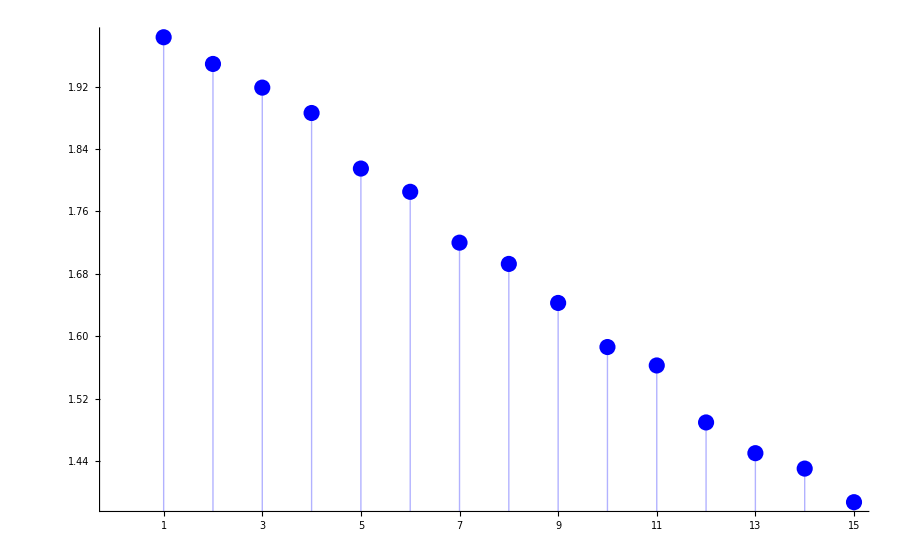

```mathematica
ListPlot[DecimalP322⟦All,3⟧+1,Joined->False,Filling->Axis,PlotStyle->{Large,Blue,Thick},Ticks->{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},Automatic},LabelStyle->Large]
```

## Construction of Cuneiform Tablet

### Functions

```mathematica
Cuneiform[n_,s_]:=If[Length[IntegerDigits[n]]>1,ImageAssemble[{ImageResize[picB⟦IntegerDigits[n]⟦1⟧⟧,s],ImageResize[picA⟦IntegerDigits[n]⟦2⟧+1⟧,s]}],
ImageResize[picA⟦IntegerDigits[n]⟦1⟧+1⟧,s]];
CuneiformBlank[n_,s_]:=If[Length[IntegerDigits[n]]>1,ImageAssemble[{ImageResize[picB⟦IntegerDigits[n]⟦1⟧⟧,s],ImageResize[picA⟦IntegerDigits[n]⟦2⟧+1⟧,s],ZeroSymbol[{s⟦1⟧/1.5,s⟦2⟧}]}],
ImageAssemble[{ImageResize[picA⟦IntegerDigits[n]⟦1⟧+1⟧,s],ZeroSymbol[{s⟦1⟧/1.5,s⟦2⟧}]}]];
```

```mathematica
ZeroSymbol[w_,h_]:=ImageResize[picA⟦1⟧,{w,h}];
ZeroSymbol[s_]:=ImageResize[picA⟦1⟧,s];
```

```mathematica
CuneiformNumber[n_,s_]:=Table[CuneiformBlank[n⟦i⟧,s],{i,Length[n]}];
```

### Full tablet

```mathematica
FullTablet={
{{1,59,0,15},{1,59},{2,49},{1}},
{{1,56,56,58,14,50,6,15},{56,7},{1,20,25},{2}},
{{1,55,7,41,15,33,45},{1,16,41},{1,50,49},{3}},
{{1,53,10,29,32,52,16},{3,31,49},{5,9,1},{4}},
{{1,48,5,1,40},{1,5},{1,37},{5}},
{{1,47,6,41,40},{5,19},{8,1},{6}},
{{1,43,11,56,28,26,40},{38,11},{59,1},{7}},
{{1,41,33,45,14,3,45},{13,19},{20,49},{8}},
{{1,38,33,36,36},{8,1},{12,49},{9}},
{{1,35,10,2,28,27,24,26},{1,22,41},{2,16,1},{10}},
{{1,33,45},{45},{1,15},{11}},
{{1,29,21,54,2,15},{27,59},{48,49},{12}},
{{1,27,0,3,45},{2,41},{4,49},{13}},
{{1,25,48,51,35,6,40},{29,31},{53,49},{14}},
{{1,23,13,46,40},{28},{53},{15}}
};
```

### Images

```mathematica
picA={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
picB={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

### Examples

```mathematica
Cuneiform[36,{50,50}]
```

-Graphics-

```mathematica
CuneiformBlank[9,{30,30}]
```

-Graphics-

```mathematica
ImageAssemble[CuneiformNumber[#,{50,50}]]&/@FullTablet⟦15⟧
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageAssemble[Table[CuneiformBlank[RandomInteger[{11,59}],{50,50}],{i,30},{j,30}]]
```

-Graphics-